```mathematica
(* FEATURES: A -> A+A, A+A -> B, A+A -> 0, B -> A, B -> 0 *)
```

```mathematica
AVOGADRO=6.0221367*10^23;
Mtoperm3[molar_]= molar*(1000*AVOGADRO);
microMtoperm3[micromolar_]= Mtoperm3[micromolar/(1*10^6)];calckD[Diffusion_,sigma_]= 4.0*Pi*Diffusion*sigma;
calcka[konvar_,kDvar_]=1/((1/konvar)-(1/kDvar));
calckd[koffvar_,konvar_,kDvar_] =calcka[konvar,kDvar]*koffvar/konvar;
```

```mathematica
NA=350.;
NB=NA/7;
L=1*10^(-6);
VOLUME=L^3;
CONCENTRATIONA=NA / VOLUME;
CONCENTRATIONB= NB / VOLUME;
```

```mathematica
DA=1.0*10^-12;
RADIUSA=5.0*10^-9;

STARTA = CONCENTRATIONA  * 10.;
STARTB = CONCENTRATIONB  *10.;

kon=1.*10^(-19)
koff=7/4. *kon* CONCENTRATIONA
kD=calckD[2*DA,2*RADIUSA];

ka=calcka[kon,kD]
kd=calckd[koff,kon,kD]

kon/koff;
ka/kd;
```

1.×10^-19

61.25

1.66082×10^-19

101.725

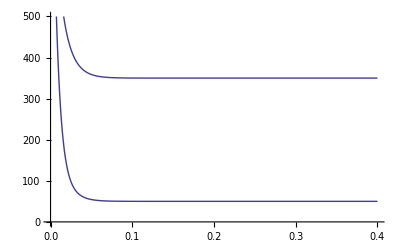

{350.}

{50.}

```mathematica
ENDTIME = 0.4;
s = NDSolve[{
A'[t]==-ka*A[t]^2-ka*A[t]^2+kd*A[t]+kd*B[t],
B'[t]==ka /2.* A[t]^2 - kd*B[t]-kd*B[t] , 
A[0]==STARTA,
B[0]==STARTB
}, {A, B}, {t, 0, ENDTIME}];
Plot[{A[t]*VOLUME, B[t]*VOLUME} /. s, {t, 0, ENDTIME},PlotRange->{0, 500}] 
A[ENDTIME]*VOLUME/.s
B[ENDTIME]*VOLUME/.s
```

```mathematica
dAdt[t_]=-2*kon*A[t]^2+koff*(A[t]+B[t]);
dBdt[t_]=kon /2.* A[t]^2 - 2*koff*B[t];
m11=D[dAdt[t], A[t]]/.A[t]->CONCENTRATIONA;
m12=D[dAdt[t], B[t]];
m21 = D[dBdt[t], A[t]]/.A[t]->CONCENTRATIONA;
m22=D[dBdt[t], B[t]];
Eigenvalues[{{m11, m12}, {m21, m22}}]
Eigenvalues[{{-9./7, 1}, {4./7, -2}}]
```

{-151.833,-49.4169}

{-2.47891,-0.806807}